# SERIES SOLUTION OF QUARK MASS RGE

```mathematica
(*Written in Mathematica 11.3. Uses Rubi 4.16.0.4.*)
```

This notebook provides code to using Rubi to calculate the perturbative series solution of the quark mass renormalization group equation.  It is intended as a supplement to the paper: Mes, Stephens, ‘An Application of Rubi: Series Expansion of the Quark MassRenormalization Group Equation’, (2018). 

Always check for the latest version in the git repository: 
https://github.com/AlexesMes/light-quark-masses . 
(This repository also contains additional resources which would be of interest to the reader.) 

Please cite the journal paper if any part of this code is used in your own research.
This work is licensed under the Creative Commons Attribution-ShareAlike 4.0 International License. To view a copy of this license, visit http://creativecommons.org/licenses/by-sa/4.0/ or send a letter to Creative Commons, PO Box 1866, Mountain View, CA 94042, USA.

Mathematica code written by A. Mes and J. Stephens
ORCID ID: 0000-0002-1187-7655 and 0000-0002-0131-703X
Corresponding email address: MSXALE002@myuct.ac.za
Last revised: 05-11-2018.

```mathematica
<<GeneralUtilities`
```

#### Installing Rubi

Rubi is a package developed by Albert Rich & Patrick Scheibe for the purpose of solving integrals using rules. 
This package (in paclet format) needs to be installed if used for the first time. Comment in the following line to install Rubi v4.16.0.4 - used in this notebook.

```mathematica
(*PacletInstall["https://github.com/RuleBasedIntegration/Rubi/releases/download/4.16.0.4/Rubi-4.16.0.4.paclet"]*)
```

#### Loading Rubi Functionality

Rubi is loaded using the following command.

```mathematica
<<Rubi`
```

## Global Inputs and Constants

```mathematica
$Assumptions-> nf∈ Reals && s0∈ Reals && s∈ Reals;
```

### QCD β-Coefficients

```mathematica
(*The known β co-efficients of QCD. Source: Baikov, Chetyrkin, Kühn, 'Five-Loop Running of the QCD coupling constant'(2017). Reference to earlier co-efficient determinations is given in this paper.*)

b0C=1/4(11-2/3 nf);
b1C=1/16(102-38/3 nf);
b2C=1/64 (2857/2 -5033/18 nf +325/54 nf^2);
b3C=1/256 (149753/6 +3564Zeta[3]-(1078361/162+6508/27 Zeta[3]) nf+(50065/162+6472/81 Zeta[3])nf^2+1093/729 nf^3);
b4C=1/4^5 (8157455/16+621885/2*Zeta[3]-88209/2*Zeta[4]-288090*Zeta[5]+nf*(-336460813/1944-4811164/81*Zeta[3]+33935/6*Zeta[4]+1358995/27*Zeta[5])+
           nf^2*(25960913/1944+698531/81*Zeta[3]-10526/9*Zeta[4]-381760/81*Zeta[5])+
nf^3*(-630559/5832-48722/243*Zeta[3]+1618/27*Zeta[4]+460/9*Zeta[5])+
nf^4*(1205/2916-152/81*Zeta[3]));
```

### QCD γ-Coefficients

```mathematica
(*The known γ co-efficients of QCD. Source: Baikov, Chetyrkin, Kühn, 'Quark Mass and Field Anomalous Dimensions to order Subscript[α, s]^5' (2014). Reference to earlier co-efficient determinations is given in this paper.*)
```

```mathematica
g0C =1;
g1C = 1/16(202/3-20/9*nf);

g2C = 1/64(1249-(2216/27+ 160/3*Zeta[3])*nf )-140/81*nf^2;

g3C = 1/256(4603055/162+135680/27*Zeta[3]-8800*Zeta[5]+(-91723/27-34192/9*Zeta[3]+880*Zeta[4] + 18400/9*Zeta[5])*nf 
    +( 5242/243+800/9*Zeta[3]-160/3*Zeta[4])*nf^2 +(-332/243+64/27*Zeta[3])*nf^3);
g4C = 1/4^5(99512327/162+46402466/243*Zeta[3]+96800*Zeta[3]^2-698126/9*Zeta[4]-231757160/243*Zeta[5]+242000*Zeta[6]+412720*Zeta[7]
   +nf*(-150736283/1458-12538016/81*Zeta[3]-75680/9*Zeta[3]^2+2038742/27*Zeta[4]+49876180/243*Zeta[5]-638000/9*Zeta[6]-1820000/27*Zeta[7])
   +nf^2*(1320742/729+2010824/243*Zeta[3]+46400/27*Zeta[3]^2-166300/27*Zeta[4]-264040/81*Zeta[5]+92000/27*Zeta[6])
   +nf^3*(91865/1458+12848/81*Zeta[3]+448/9*Zeta[4]-5120/27*Zeta[5])+nf^4*(-260/243-320/243*Zeta[3]+64/27*Zeta[4]));
```

## Renormalization Group Equations

In QCD,as in Quantum Electrodynamics (QED),one removes the present divergences with a technique known as renormalization. A nonphysical renormalization scale parameter,μ,is introduced in the renormalization procedure to represent the point at which one performs the subtraction of the divergences to render the amplitudes finite. Both the renormalized coupling α_s(μ^2),and the quark masses,m_q(μ^2),depend on the defining renormalization scheme,and on the scale parameter,μ.

## RGE for the running strong coupling, α(μ)

The renormalization group equation for a(s) = (α(s))/π , is given by: (d a(s))/(d ln(s))=β(a(s))=−a^2(s)(β0 + a(s)β1 + a^2(s)β2 + a^3(s)β3 + a^4(s)β4). 
The perturbative series solution  for the running coupling constant,a(s)is given below.  This equation can be used to determine the running coupling constant at any chosen scale s,where a(s) is known at some reference scale s0. Source: Davier, Hocker, Zhang, 'The physics of hadronic tau decays'(2005).

```mathematica
as[s_,a0_,s0_]:=
a0 +a0^2*(-b0*Log[s/s0]) +a0^3*(-b1*Log[s/s0] + b0^2*(Log[s/s0])^2)+a0^4*(-b2*Log[s/s0] +5/2 *b0*b1*(Log[s/s0])^2-b0^3*(Log[s/s0])^3)  +a0^5*(-b3*Log[s/s0] +3/2 *b1^2*(Log[s/s0])^2+3*b0*b2*(Log[s/s0])^2 -13/3*b0^2*b1*Log[s/s0]^3+ b0^4*(Log[s/s0])^4)+a0^6*(-b4*Log[s/s0]+7/2*b0*b1*(Log[s/s0])^2+7/2*b0*b3*(Log[s/s0])^2-35/6*b0*b1^2*(Log[s/s0])^3-6*b0^2*b2*(Log[s/s0])^3+77/12*b0^3*b1*(Log[s/s0])^4-b0^5*(Log[s/s0])^5);
```

## RGE for the running quark mass, m(s)

The renormalization group equation for  m_q(s) , is given by:  1/(m_q(s))(d m_q(s))/(d ln(s))=γ(a(s))=−a(s)(γ0 + a(s)γ1 + a^2(s)γ2 + a^3(s)γ3 + a^4(s)γ4). 
This is a  linear seperable differential equation.  It can be rearrranged : 
m_q(s) =m_q(s0) *Exp(∫da'_s(γ(a'_s))/(β(a'_s)))  =  m_q(s0) *Exp(∫da'_s(γ0 +  a'_s γ1  +  a'_s^2 γ2 + a'_s^3 γ3  +  a'_s^4 γ4)/(a'_s β0 + a'_s^2 β1 + a'_s^3 β2 + a'_s^4 β3 + a'_s^5 β4)) ,  with  a_s(s) and a_s(s0) as the upper and lower bounds of the integral, respectively. 

We aim to calculate the perturbative series solution  for the running quark mass, m_q (s).  This is an alternative to directly integrating the  defining quark mass renormalization group equation given above.

```mathematica
integrand[x_]=(g0+ x*g1 + x^2*g2+x^3*g3 + x^4*g4)/(x*b0+x^2*b1+x^3*b2+x^4*b3+x^5*b4);
```

```mathematica
(*Indefinite integral of (γ(Subscript[a, s]))/(β(Subscript[a, s])) performed using Rubi. Int[] is a built-in Rubi command.*)
rindef=Int[integrand[x],x]
```

(g0 Log[x])/b0-((b4 g0-b0 g4) Log[b0+b1 x+b2 x^2+b3 x^3+b4 x^4])/(4 b0 b4)-((3 b1 b4 g0-4 b0 b4 g1+b0 b1 g4) Int[1/(b0+b1 x+b2 x^2+b3 x^3+b4 x^4),x])/(4 b0 b4)-((b2 b4 g0-2 b0 b4 g2+b0 b2 g4) Int[x/(b0+b1 x+b2 x^2+b3 x^3+b4 x^4),x])/(2 b0 b4)-((b3 b4 g0-4 b0 b4 g3+3 b0 b3 g4) Int[x^2/(b0+b1 x+b2 x^2+b3 x^3+b4 x^4),x])/(4 b0 b4)

```mathematica
(*Replacing Int[] Rubi command with Mathematica's Integrate[] command - in order to proceed with the calculation in Mathematica.*)rubiindef=(g0 Log[x])/b0-((b4 g0-b0 g4) Log[b0+b1 x+b2 x^2+b3 x^3+b4 x^4])/(4 b0 b4)-((3 b1 b4 g0-4 b0 b4 g1+b0 b1 g4) Integrate[1/(b0+b1 x+b2 x^2+b3 x^3+b4 x^4),x])/(4 b0 b4)-((b2 b4 g0-2 b0 b4 g2+b0 b2 g4) Integrate[x/(b0+b1 x+b2 x^2+b3 x^3+b4 x^4),x])/(2 b0 b4)-((b3 b4 g0-4 b0 b4 g3+3 b0 b3 g4) Integrate[x^2/(b0+b1 x+b2 x^2+b3 x^3+b4 x^4),x])/(4 b0 b4) ;
```

```mathematica
(*Turning the indefinite integral of (γ(Subscript[a, s]))/(β(Subscript[a, s])) into a definite integral with Subscript[a, s](s) and Subscript[a, s](s0) as the upper and lower bounds of the integral, respectively.*)
rubidef [s_]=  ExpandAll[(rubiindef/.x->as[s,a0,s0])-(rubiindef/.x->a0)] ;
```

```mathematica
(*Exponentiating and Taylor expanding the definite integral in order to find the perturbative series solution for the running quark mass to five-loop order.*)
qmassseries5[s_] =Collect[(Series[Exp[rubidef [s]],{a0,0,5}]), a0, Simplify]
```

1-a0 g0 Log[s/s0]+1/2 a0^2 Log[s/s0] (-2 g1+g0 (b0+g0) Log[s/s0])-1/6 a0^3 Log[s/s0] (6 g2-3 (b1 g0+2 (b0+g0) g1) Log[s/s0]+g0 (2 b0^2+3 b0 g0+g0^2) Log[s/s0]^2)+1/24 a0^4 Log[s/s0] (-24 g3+12 (b2 g0+2 b1 g1+g1^2+3 b0 g2+2 g0 g2) Log[s/s0]-4 (6 b0^2 g1+3 g0^2 (b1+g1)+b0 g0 (5 b1+9 g1)) Log[s/s0]^2+g0 (6 b0^3+11 b0^2 g0+6 b0 g0^2+g0^3) Log[s/s0]^3)+1/120 a0^5 Log[s/s0] (-120 g4+(60 (-7 b1 b2 g0+4 b0^2 g3+b0 (7 b1 g0+b3 g0+2 b2 g1+3 b1 g2+2 g1 g2+2 g0 g3)) Log[s/s0])/b0-20 (3 b1^2 g0+b1 (14 b0+9 g0) g1+3 (2 b0+g0) (b2 g0+g1^2+2 b0 g2+g0 g2)) Log[s/s0]^2+10 (12 b0^3 g1+g0^3 (3 b1+2 g1)+b0 g0^2 (13 b1+12 g1)+b0^2 g0 (13 b1+22 g1)) Log[s/s0]^3-g0 (24 b0^4+50 b0^3 g0+35 b0^2 g0^2+10 b0 g0^3+g0^4) Log[s/s0]^4)

```mathematica
(*A tidied version of the series expansion qmassseries5[s], with the relevant terms collected and factorized.*)
jamsseries5 [s_]= 1- a0 g0 Log[s/s0]+ a0^2 Log[s/s0](g0/2(b0+g0)Log[s/s0]-g1) + a0^3 Log[s/s0]((-g0^3/6-(b0*g0)(b0/3 + g0/2))Log[s/s0]^2+ ((b1 g0)/2 + g1(b0 + g0))Log[s/s0] - g2)+ a0^4 Log[s/s0]((g0^4/24+b0*g0/4*(11*b0*g0/6+b0^2+g0^2))Log[s/s0]^3  + (-b0^2*g1 -g0^2/2*(b1+g1)-1/6*b0*g0*(5b1+9g1))Log[s/s0]^2+ ((b2*g0)/2 + g1(b1 + g1/2) + g2(3/2 b0 + g0))Log[s/s0] - g3)+ a0^5 Log[s/s0](-g4+((-7 b1/2(b2/b0-1)+b3/2)g0+b2*g1+(g1+3/2*b1)*g2+(2*b0+g0)g3)Log[s/s0]+((-b1^2*g0)/2-(b0+g0/2)(b2*g0+g1^2+2*b0*g2+g0*g2)-(b1*g1)/6(14b0+9g0))Log[s/s0]^2 +(b0^3 g1+g0^3(b1/4+g1/6)+b0*g0^2(13/12*b1+g1)+(b0^2*g0)/12*(13*b1+22g1))Log[s/s0]^3+(-g0/120(g0^4+10*g0^3 b0+35*g0^2*b0^2+50 b0^3*g0+24*b0^4))Log[s/s0]^4);
```

```mathematica
(*Comparison to see if the two expressions are equivalent*)
FullSimplify[jamsseries5 [s]] === FullSimplify[qmassseries5[s]]
```

True

### Comparing with Chetyrkin et al. (1997) and Kniehl (1996)

qmassseries5[s]  gives the perturbative series solution of the quark mass RG equation to five-loop order.  In this section we check whether the seriesexp5[s] agrees to the fourth-loop with Chetyrkin et al. (Source: Chetyrkin,K.,Kniehl,B.A.,Sirlin,A.,1997. Estimations of order α_s^3  andα_s^4 corrections to mass-dependent observables.Physics Letters B 402 (3-4),359–366).
Note: Kniehl (Source:Kniehl,B.A.,1996. Dependence of electroweak parameters on the definition of the top-quark mass. Zeitschrift furPhysik C:Particles and Fields 72 (3),437) which gives the mass series solution up to three-loop order agrees exactly with Chetyrkin et al.(1997)  up to three-loop order.

```mathematica
(*The perturbative series solution for the running quark mass given by qmassseries4[s] to four-loop order.*)
qmassseries4[s_] =qmassseries5[s] // Function[y, Normal[y+ O[a0]^5]]
```

1-a0 g0 Log[s/s0]+1/2 a0^2 Log[s/s0] (-2 g1+g0 (b0+g0) Log[s/s0])-1/6 a0^3 Log[s/s0] (6 g2-3 (b1 g0+2 (b0+g0) g1) Log[s/s0]+g0 (2 b0^2+3 b0 g0+g0^2) Log[s/s0]^2)+1/24 a0^4 Log[s/s0] (-24 g3+12 (b2 g0+2 b1 g1+g1^2+3 b0 g2+2 g0 g2) Log[s/s0]-4 (6 b0^2 g1+3 g0^2 (b1+g1)+b0 g0 (5 b1+9 g1)) Log[s/s0]^2+g0 (6 b0^3+11 b0^2 g0+6 b0 g0^2+g0^3) Log[s/s0]^3)

```mathematica
(*The perturbative series solution given to three-loop order in Kniel (1996) and to four-loop order by Chetyrkin et al. (1997).*)chetyrkin = 1- a0 g0 Log[s/s0]+ (a0^2)Log[s/s0]((g0/2)(b0+g0)Log[s/s0]-g1) + (a0^3)Log[s/s0](-(g0/3)(b0+g0)(b0 + g0/2)Log[s/s0]^2 + (b1 g0/2 + g1(b0 + g0))Log[s/s0] - g2) + (a0^4)Log[s/s0]((g0/4) (b0 + g0)(b0 + g0/2)(b0 + g0/3)(Log[s/s0])^3  - ((b1*g0 /2 )(5/3 b0 + g0) + g1 (b0+ g0)( b0 + g0/2))(Log[s/s0])^2 + ((b2*g0 /2 )+ g1(b1 + g1/2) + g2(3/2 b0 + g0))Log[s/s0] - g3);
```

```mathematica
(*Comparison to see if the two expressions are equivalent*)
FullSimplify[qmassseries4[s]] === FullSimplify[chetyrkin]
```

True

## Numerical Evaluation

In this section we compare the effect of the fifth-loop term in the series solution. To do this we compare qmassseries5[s]  with the four-loop series determined by Chetyrkin et al.(1997)

```mathematica
(*Setting the γ(Subscript[a, s]) and β(Subscript[a, s]) coefficients to their numerical values*)
{g0,g1,g2,g3,g4,b0,b1,b2,b3,b4}={g0C,g1C,g2C,g3C,g4C,b0C,b1C,b2C,b3C,b4C};
```

```mathematica
(*Inserting the values of the γ(Subscript[a, s]) and β(Subscript[a, s]) coefficients into the quark mass series solution to five-loop order*)
numseries5[s_,ms0_]=ms0*Normal[FullSimplify[qmassseries5[s]]]
```

ms0 (1+1/(52254720 (-33+2 nf))a0 Log[s/s0] ((-33+2 nf) (-52254720+725760 a0 (-303+10 nf)+10080 a0^2 (-101169+8 nf (831+1120 nf))+a0^4 (35 (-895610943+nf (150736283+nf (-2641484+5 nf (-18373+312 nf))))-42 (-1047189+nf (1019371+2 nf (-41575+16 nf (21+nf)))) π^4-4000 (-33+2 nf) (-99+23 nf) π^6)+420 a0^3 (-13809165+2 nf (825507-5242 nf+332 nf^2+72 (-33+2 nf) π^4)))+14 a0 (30 a0^2 (-33+2 nf) (-18 (-45+2 nf) (-39+2 nf) (-37+2 nf)+a0 (28734588+nf (-5652189+4 nf (95844+nf (-2557+20 nf))))) Log[s/s0]^3-72 a0^3 (-18+nf) (-45+2 nf) (-39+2 nf) (-37+2 nf) (-33+2 nf) Log[s/s0]^4+10 a0 (-33+2 nf) Log[s/s0]^2 (-864 (-45+2 nf) (-39+2 nf)+36 a0 (-716283+4 nf (25137+2 nf (-504+5 nf)))+a0^2 (-289295550+nf (53340633+10650447 nf-1348158 nf^2+35840 nf^3+4320 (39-2 nf)^2 Zeta[3])))+5 Log[s/s0] (-31104 (-45+2 nf) (-33+2 nf)+864 a0 (-33+2 nf) (16389+2 nf (-699+10 nf))+18 a0^2 (-33+2 nf) (6090615+2 nf (-382314-173577 nf+8960 nf^2+2160 (-41+2 nf) Zeta[3]))+a0^3 (-23995998846+5324224149 nf+204988062 nf^2-80188962 nf^3+3270040 nf^4+2656 nf^5-6115824 nf π^4+1054944 nf^2 π^4-60480 nf^3 π^4+1152 nf^4 π^4-72 (-33+2 nf) (-1395051+nf (1191817+2 nf (-43883+16 nf (18+nf)))) Zeta[3]-43200 (-39+2 nf) (-33+2 nf) (-99+23 nf) Zeta[5]))+30 a0 (-33+2 nf) (103680 nf Zeta[3]+288 a0 (-(8480+nf (-6411+2 nf (75+2 nf))) Zeta[3]+150 (99-23 nf) Zeta[5])+a0^2 ((-23201233+4 nf (4701756+nf (-251353-4818 nf+40 nf^2))) Zeta[3]-720 (16335+nf (-1419+290 nf)) Zeta[3]^2+10 (11587858+nf (-2493809+6 nf (6601+384 nf))) Zeta[5]+2520 (-19899+3250 nf) Zeta[7])))))

```mathematica
(*Inserting the values of the γ(Subscript[a, s]) and β(Subscript[a, s]) coefficients into the quark mass series solution to the fourth order (i.e. Chetyrkin et al.).*)
numseries4[s_,ms0_]=ms0*Normal[FullSimplify[qmassseries4[s]]]
```

ms0 (1+1/124416 a0 Log[s/s0] (-124416+a0 (1728 (-303+10 nf)+a0 (-2428056-13809165 a0+192 nf (831+1120 nf)+2 a0 nf (825507-5242 nf+332 nf^2+72 (-33+2 nf) π^4)))+3 a0 (4 a0 (-81 (520+8843 a0)+252 (16+399 a0) nf-96 (1+42 a0) nf^2+40 a0 nf^3) Log[s/s0]^2-6 a0^2 (-45+2 nf) (-39+2 nf) (-37+2 nf) Log[s/s0]^3+Log[s/s0] (1728 (45-2 nf)+a0 (786672+96 nf (-699+10 nf)+a0 (6090615+2 nf (-382314-173577 nf+8960 nf^2+2160 (-41+2 nf) Zeta[3]))))+96 a0 (360 nf Zeta[3]-a0 (8480+nf (-6411+2 nf (75+2 nf))) Zeta[3]+150 a0 (99-23 nf) Zeta[5]))))

### Initialize Constants

```mathematica
nf=3; (*for three light quark flavours*)

(*s0 = (mτ)^2 = initial reference energy (i.e. the tau-lepton mass scale), a0 = (coupling strength at s=s0)/π,uncert0 = (uncertainty in coupling strength at s=s0)/π. 
Source: Antonio Pich, 'Precision physics with QCD'.137:01016 (2017).*)
s0 = (1.77686)^2;alpha0= 0.328; a0=alpha0/Pi;uncertalpha0 = 0.013; uncert0=uncertalpha0/Pi;

mud0=3.86; (*̄As an example, use the mass of the up- and down- quark as the initial value: Subscript[m, ud](2 GeV)=(3.86±0.2)MeV. Source: Cesareo Dominguez, Alexes Mes, Karl Schilcher,'Up-and down-quark masses from QCD sum rules'.arXiv preprintarXiv:1809.07042 (2018).*)

srange = Range[1,5,0.001]; (*The energy scale parameter s is taken to vary between 1 GeV^2 and 5 GeV^2*)
```

### Direct Integration

Since the quark mass is a linear seperable differential equation, we are able to  directly integrate the differential RG equation to find the running quark mass through numerical means.

```mathematica
qmassdirectint[s_,ms0_]:=ms0*Exp[NIntegrate[integrand[a],{a,a0,as[s,a0,s0]}]];
```

### Graphical Output

```mathematica
SetOptions[Plot,PlotStyle->ColorData[112]]; (*This sets the colour to a different pallette*)
```

```mathematica
(*Plotting the perturbative series solution to four-loop order (Chetyrkin et al.,1997),the perturbative series solution to five-loop order (jamsseries5), and the direct numerical integration (qmassdirectint[s,ms0]), over a range s = 1 GeV^2-5 GeV^2 and s = 1 GeV^2 - 1.5 GeV^2.*)

qmassdirectintOutput=ParallelTable[{s,Evaluate[qmassdirectint[s,mud0]]},{s,srange}];
numseries5Output=ParallelTable[{s,Evaluate[numseries5[s,mud0]]},{s,srange}];
numseries4Output=ParallelTable[{s,Evaluate[numseries4[s,mud0]]},{s,srange}];

massgraphRGE=ListLinePlot[{numseries4Output,numseries5Output, qmassdirectintOutput},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","m_ud((2 GeV)^2) (MeV)"},PlotLegends->LineLegend[Automatic,{"4 loop series", "5 loop series", "5 loop numerical integration"}],PlotStyle -> {Directive[Thickness[0.0035]], Directive[Thickness[0.0035],Orange],Directive[Thickness[0.0035]]} ,PlotRange-> {{1,5},{3.6,4.8}}]
Export[FileNameJoin[{NotebookDirectory[],"RGEmassgraph.pdf"}],massgraphRGE];
```

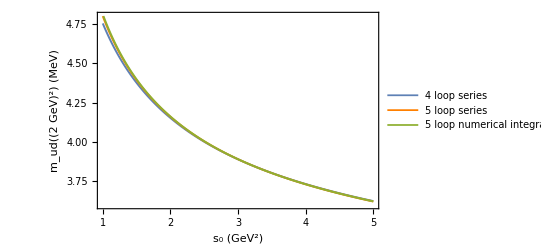
```mathematica
-Graphics-;
```

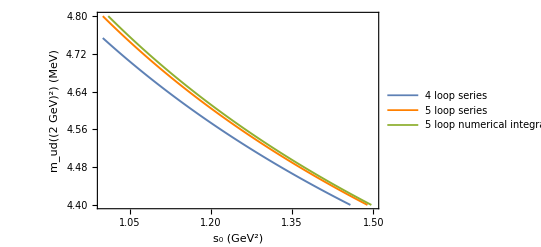
```mathematica
-Graphics-;
```

```mathematica
(*It is more lucid to provide a local error analysis by plotting the difference between the direct numerical integration (qmassdirectint[s,ms0])and i).the perturbative series solution to five-loop order (jamsseries5), ii).the perturbative series solution to four-loop order (Chetyrkin et al.,1997). *)

numseries5difference =ParallelTable[{s,Evaluate[qmassdirectint[s,mud0]-numseries5[s,mud0]]},{s,srange}]; 
numseries4difference =ParallelTable[{s,Evaluate[qmassdirectint[s,mud0]-numseries4[s,mud0]]},{s,srange}]; 

massgraphRGE2=ListLinePlot[{numseries4difference,numseries5difference},Frame-> True,FrameStyle->Thick,FrameLabel-> {"s_0 (GeV^2)","Diffence between series and numerical solution (MeV)"},PlotLegends->LineLegend[Automatic,{"4 loop series", "5 loop series"}],PlotStyle -> {Directive[Thickness[0.00354]], Directive[Thickness[0.00354],Orange]} ,PlotRange-> {{1,5},{-0.002,0.013}}]
Export[FileNameJoin[{NotebookDirectory[],"RGEmassgraphDifference.pdf"}],massgraphRGE2];
```

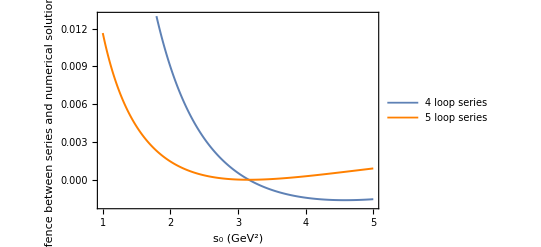
```mathematica
-Graphics-;
```

## Statistical Analysis

In this section we compare the effect of the fifth-loop term in the series solution, using two common statistical evaluation criteria:Root Mean Absolute Error (RMSE) andMean Absolute Error (MAE) are used. The Root Mean Absolute Error is defined as RMSE=√1/n(∑^n)_(j=1)(r_j−k_j)^2,and the Mean Absolute Error is calculated as MAE=1/n(∑^n)_(j=1)|r_j−k_j|.

```mathematica
refseries = qmassdirectintOutput;
n = Length[refseries];
```

```mathematica
(*Root Mean Absolute Error*)
rmse5Output =Sqrt[(1/n)Total[(numseries5Output - refseries)^2][[2]]]
rmse4Output =Sqrt[(1/n)Total[(numseries4Output - refseries)^2][[2]]]
```

0.0028758
0.0146155

```mathematica
(*Mean Absolute Error*)
mae5Output =(1/n)Total[Abs[(numseries5Output - refseries)]][[2]]
mae4Output =(1/n)Total[Abs[(numseries4Output - refseries)]][[2]]
```

0.00152145
0.00790016

```mathematica
(* Smallest Deviations*)
smallest5Output =Min[Abs[(numseries5Output - refseries)[[2]]]]
smallest4Output =Min[Abs[(numseries4Output - refseries)[[2]]]]
```

0.
0.

```mathematica
(* Largest Deviations*)
smallest5Output =Max[Abs[(numseries5Output - refseries)[[2]]]]
smallest4Output =Max[Abs[(numseries4Output - refseries)[[2]]]]
```

0.0116077
0.0578165

## Comparison to using Mathematica without Rubi

In this section we  attempt to solve the same problem (i.e. finding the running quark mass pertubative series solution  to five-loop order) by only using Mathematica's built-in integration function i.e. without using Rubi.

```mathematica
Clear[g0,g1,g2,g3,g4,b0,b1,b2,b3,b4,a0,s0];
```

### Attempt 1 : Using Mathematica' s built - in Integrate[] function

Mathematica seems unable to find the series expansion in a single step. Uncomment the first line of code in this subsection to try this. 
Breaking the process up into seperate steps: indefinite integral, definite integral, exponentiating, taylor expanding. We see that the issue is aready present in the indefinite integral (intef): i.e. Mathematica immediately aproximates the integral of γ(a_s)/β(a_s) with a RootSum object which contains logarithmic diverges. From here, Mathematica struggles to compute the definite integral and then the taylor series (these last two lines of code in this subsection are commented).

```mathematica
(*The first line of code in this subsection tries to find the series solution in a single step. Uncomment the line of code to try this. *)
(*Collect[Series[Exp[Integrate[(g0 + a*g1 + a^2*g2+a^3*g3 + a^4*g4)/(a*b0 + a^2*b1+a^3*b2+a^4*b3+a^5*b4),{a,a0,as[s,a0,s0]}]],{a0,0,5}],a0, Simplify]*)
```

```mathematica
intef=Integrate[integrand[x],x]
```

(g0 Log[x])/b0-1/b0 RootSum[b0+b1 #1+b2 #1^2+b3 #1^3+b4 #1^4&,1/(b1+2 b2 #1+3 b3 #1^2+4 b4 #1^3)(b1 g0 Log[x-#1]-b0 g1 Log[x-#1]+b2 g0 Log[x-#1] #1-b0 g2 Log[x-#1] #1+b3 g0 Log[x-#1] #1^2-b0 g3 Log[x-#1] #1^2+b4 g0 Log[x-#1] #1^3-b0 g4 Log[x-#1] #1^3)&]

```mathematica
(*These two code lines (which perform the definite integral and taylor expansion) are commented since Mathematica struggles to compute them. Uncomment to try*)
(*defintef[s_]=  ExpandAll[(intef/.x->as[s,a0,s0])-(intef/.x->a0)];
qmassseries5M[s_] =Collect[(Series[Exp[defintef[s]],{a0,0,5}]), a0, Simplify]*)
```

### Attempt 2 : Using a pure function in Mathematica

In comparison to the first attempt, Mathematica is able to process the integral of the pure function with greater ease. However, we can easily see the present infinities in the  RootSum object resulting from the indefinite integral (intepf).  This translates to unevaluated sections (0&)  present in the final series solution.
The first line of code in this subsection tries to find the series solution in a single step. Uncomment the line of code to try this.

```mathematica
(*The first line of code in this subsection tries to find the series solution in a single step. Uncomment the line of code to try this. *)
(*Collect[Series[Exp[Evaluate[Integrate[(g0 + a*g1 + a^2*g2+a^3*g3 + a^4*g4)/(a*b0 + a^2*b1+a^3*b2+a^4*b3+a^5*b4),{a,a0,as[s,a0,s0]}]/.a->(#)]&],{a0,0,5}],a0, Simplify]*)
```

```mathematica
purefunc = ((g0 + #*g1 + #^2*g2+#^3*g3 + #^4*g4)/(#*b0 + #^2*b1+#^3*b2+#^4*b3+#^5*b4))&;
```

```mathematica
intepf=Derivative[-1][purefunc]
```

(g0 Log[#1])/b0-RootSum[b0+b1 #1+b2 #1^2+b3 #1^3+b4 #1^4&,(b1 g0 (-∞)+b0 g1 ∞+b0 g3 ∞ Sign[#1]^2+b0 g4 ∞ Sign[#1]^3+b2 g0 (-∞) #1+b0 g2 ∞ #1+b3 g0 (-∞) #1^2+b4 g0 (-∞) #1^3)/(b1+2 b2 #1+3 b3 #1^2+4 b4 #1^3)&]/b0&

```mathematica
defintepf[s_]=  ExpandAll[(intepf/.#1->as[s,a0,s0])-(intepf/.#1->a0)];
```

```mathematica
qmassseries5Mpf[s_] =Collect[(Series[Exp[defintepf[s]],{a0,0,5}]), a0, Simplify]
```

1-a0 g0 (0&) Log[s/s0]+(a0^2 g0 (0&) Log[s/s0] (-2 b1+b0 (b0+g0+g0 (0&)) Log[s/s0]))/(2 b0)-(a0^3 g0 (0&) Log[s/s0] (6 b2-3 b1 (3 b0+2 g0 (1+(0&))) Log[s/s0]+b0 (2 b0^2+3 b0 g0 (1+(0&))+g0^2 (1+3 (0&)+(0&)^2)) Log[s/s0]^2))/(6 b0)+1/(24 b0^2)a0^4 g0 (0&) Log[s/s0] (-24 b0 b3+12 (b1^2+2 b0 b2) (2 b0+g0+g0 (0&)) Log[s/s0]-4 b0 b1 (11 b0^2+12 b0 g0 (1+(0&))+3 g0^2 (1+3 (0&)+(0&)^2)) Log[s/s0]^2+b0^2 (6 b0^3+11 b0^2 g0 (1+(0&))+6 b0 g0^2 (1+3 (0&)+(0&)^2)+g0^3 (1+7 (0&)+6 (0&)^2+(0&)^3)) Log[s/s0]^3)-1/(120 b0^2)a0^5 g0 (0&) Log[s/s0] (120 b0 b4-60 (-2 b0 b1 b2+b0^2 (7 b1+5 b3)+2 b1 b2 g0 (1+(0&))+2 b0 b3 g0 (1+(0&))) Log[s/s0]+20 (18 b0^3 b2+3 b1^2 g0^2 (1+3 (0&)+(0&)^2)+b0^2 (17 b1^2+15 b2 g0 (1+(0&)))+3 b0 g0 (5 b1^2 (1+(0&))+b2 g0 (1+3 (0&)+(0&)^2))) Log[s/s0]^2-10 b0 b1 (25 b0^3+35 b0^2 g0 (1+(0&))+15 b0 g0^2 (1+3 (0&)+(0&)^2)+2 g0^3 (1+7 (0&)+6 (0&)^2+(0&)^3)) Log[s/s0]^3+b0^2 (24 b0^4+50 b0^3 g0 (1+(0&))+35 b0^2 g0^2 (1+3 (0&)+(0&)^2)+10 b0 g0^3 (1+7 (0&)+6 (0&)^2+(0&)^3)+g0^4 (1+15 (0&)+25 (0&)^2+10 (0&)^3+(0&)^4)) Log[s/s0]^4)

## Validation of Results: Interchanging limiting processes in Mathematica

Here we  find the perturbative series solution by interchanging the two limiting processes i.e. the integrand is replaced with its Taylor expansion,and integrated term by term in Mathematica (without using Rubi) .

```mathematica
intetaylor=Integrate[Series[integrand[a],{a,0,5}],a]// Function[y, Normal[y+ O[a0]^6]]
```

(a (-b1 g0+b0 g1))/b0^2+(a^2 (b1^2 g0-b0 b2 g0-b0 b1 g1+b0^2 g2))/(2 b0^3)+(a^3 (-b1^3 g0+b0 b1^2 g1+b0 b1 (2 b2 g0-b0 g2)+b0^2 (-b3 g0-b2 g1+b0 g3)))/(3 b0^4)+1/(5 b0^6)a^5 (-b1^5 g0+b0 b1^4 g1+b0 b1^3 (4 b2 g0-b0 g2)+b0^2 b1^2 (-3 b3 g0-3 b2 g1+b0 g3)-b0^3 (-2 b2 b3 g0-b2^2 g1+b0 b4 g1+b0 b3 g2+b0 b2 g3)+b0^2 b1 (-3 b2^2 g0+2 b0 b2 g2+b0 (2 b4 g0+2 b3 g1-b0 g4)))+1/(6 b0^7)a^6 (b1^6 g0-b0 b1^5 g1+b0 b1^4 (-5 b2 g0+b0 g2)+b0^2 b1^3 (4 b3 g0+4 b2 g1-b0 g3)+b0^3 b1 (-6 b2 b3 g0-3 b2^2 g1+2 b0 b4 g1+2 b0 b3 g2+2 b0 b2 g3)+b0^2 b1^2 (6 b2^2 g0-3 b0 b2 g2+b0 (-3 b4 g0-3 b3 g1+b0 g4))-b0^3 (b2^3 g0-b0 b2^2 g2+b0 (-b3^2 g0+b0 b4 g2+b0 b3 g3)+b0 b2 (-2 b4 g0-2 b3 g1+b0 g4)))+(a^4 (b1^4 g0-b0 b1^3 g1+b0 b1^2 (-3 b2 g0+b0 g2)+b0^2 b1 (2 b3 g0+2 b2 g1-b0 g3)+b0^2 (b2^2 g0-b0 b2 g2+b0 (-b4 g0-b3 g1+b0 g4))))/(4 b0^5)+(g0 Log[a])/b0

```mathematica
defintetaylor[s_]=  ExpandAll[(intetaylor/.a->as[s,a0,s0])-(intetaylor/.a->a0)];
```

```mathematica
qmassseries5taylor[s_] =Collect[(Series[Exp[defintetaylor[s]],{a0,0,5}]), a0, Simplify]
```

1-a0 g0 Log[s/s0]+1/2 a0^2 Log[s/s0] (-2 g1+g0 (b0+g0) Log[s/s0])-1/6 a0^3 Log[s/s0] (6 g2-3 (b1 g0+2 (b0+g0) g1) Log[s/s0]+g0 (2 b0^2+3 b0 g0+g0^2) Log[s/s0]^2)+1/24 a0^4 Log[s/s0] (-24 g3+12 (b2 g0+2 b1 g1+g1^2+3 b0 g2+2 g0 g2) Log[s/s0]-4 (6 b0^2 g1+3 g0^2 (b1+g1)+b0 g0 (5 b1+9 g1)) Log[s/s0]^2+g0 (6 b0^3+11 b0^2 g0+6 b0 g0^2+g0^3) Log[s/s0]^3)+1/120 a0^5 Log[s/s0] (-120 g4+(60 (-7 b1 b2 g0+4 b0^2 g3+b0 (7 b1 g0+b3 g0+2 b2 g1+3 b1 g2+2 g1 g2+2 g0 g3)) Log[s/s0])/b0-20 (3 b1^2 g0+b1 (14 b0+9 g0) g1+3 (2 b0+g0) (b2 g0+g1^2+2 b0 g2+g0 g2)) Log[s/s0]^2+10 (12 b0^3 g1+g0^3 (3 b1+2 g1)+b0 g0^2 (13 b1+12 g1)+b0^2 g0 (13 b1+22 g1)) Log[s/s0]^3-g0 (24 b0^4+50 b0^3 g0+35 b0^2 g0^2+10 b0 g0^3+g0^4) Log[s/s0]^4)

```mathematica
(*Comparison to see if the two expressions are equivalent*)
FullSimplify[qmassseries5[s]] === FullSimplify[qmassseries5taylor[s]]
```

True

In this section Mathematica suceeds in calculating the perturbative series solution of the quark mass RG equation to five-loop order. The method relies on: i). interchanging the limiting processes(performing the series expansion before integration), ii). calculating the indefinite integral, followed by using the FTC to find the definite integral, iii).  performing a second taylor expansion after exponentiating the resultant integral. 
While this is nonintuitive, it does provide validation: the series solution to five-loop order determined in this subsection (qmassseries5taylor[s])  is in perfect agreement with the solution determined through using Rubi (qmassseries5[s]). 
The case for using Rubi in this situation , and in other Science, Technology, Engineering and Mathematics (STEM) research areas, is thus: it provides a lucid and intuitive aproach to solving integrals, which Mathematica is often unable to solve directly.